# Cell Complex Thinning

CSE 554 Module 2, Washington University in St. Louis (Fall 2018)

## Introduction

Thinning is one of the most commonly used methods for extracting skeletons of a solid object. Here you will experiment with thinning on 2D and 3D binary pictures using a geometric representation called Cell Complexes. This representation allows you to write simple thinning code that works on objects in any dimensions.

## Helpers

### Importing images

Sets the default folder to be the folder where this notebook is saved.

```mathematica
SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];
```

Constructs a 2D array from input RGB color images by extracting the Red component of each pixel.

```mathematica
PNGtoGray[filename_]:=Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
```

```mathematica
GIFtoGray[filename_]:=255-Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
```

### Showing images

Shows a binary image (with only values 0, 1)

```mathematica
showBinaryImage[bimg_]:=Graphics[Raster[bimg],Frame->False];
```

Shows a grayscale image

```mathematica
showGrayImage[img_]:=Graphics[Raster[img/Max[img]],Frame->False];
```

### Showing cell complexes

#### Some helper functions

Given a list of edges around the face, each as a pair of vertex indices, returns a single list of vertex indices that trace the face boundary:

```mathematica
traceFace[edgelist_]:=Module[{face=edgelist⟦1⟧,p,nlist=Drop[edgelist,1]},
While[Length[nlist]>1,
p=Position[nlist,Last[face]];
AppendTo[face,nlist⟦p⟦1,1⟧,3-p⟦1,2⟧⟧];
nlist=Drop[nlist,{p⟦1,1⟧}]];
face];
```

This function gets the scale of the cell complex (as the length of the largest side of the bounding box), for properly scaling the size of visual elements like point sizes and edge thickness:

```mathematica
getScale[cc_]:=Max[Map[(Max[#]-Min[#]+1)&,Transpose[cc⟦1⟧]]];
```

Obtains the exterior faces of a 3D complex for faster visulization:

```mathematica
getExteriorFaces[cc_]:=Module[{val},
val=Map[0&,cc⟦3⟧];
Scan[Scan[val⟦#⟧++&,#]&,cc⟦4⟧];
Pick[cc⟦3⟧,Map[(#<2)&,val]]];
```

#### 2D

Options for 2D visualization:

```mathematica
ptSize2D=0.02;ptColor2D=GrayLevel[0];ptColorOri2D=GrayLevel[0.85];
edgeSize2D=0.01;edgeColor2D=GrayLevel[.2];edgeColorOri2D=GrayLevel[0.9];faceColor2D=GrayLevel[0.5];faceColorOri2D=GrayLevel[0.95];
```

Shows a 2D cell complex:

```mathematica
showCC2D[cc_]:=Module[{scl=getScale[cc]/10.0,len=Length[cc]},
Graphics[{
If[len≥3,{faceColor2D,EdgeForm[{}],Map[Polygon[cc⟦1,traceFace[cc⟦2,#⟧]⟧]&,cc⟦3⟧]},{}],
If[len≥2,{edgeColor2D,Thickness[edgeSize2D/scl],Map[Line[cc⟦1,#⟧]&,cc⟦2⟧]},{}],
{ptColor2D,PointSize[ptSize2D/scl],Map[Point,cc⟦1⟧]}}]];
```

Shows one 2D cell complex (cc1) overlaying another (cc2), with cc2 drawn in lighter colors in the backbround:

```mathematica
showCC2D[cc1_,cc2_]:=Module[{scl=getScale[cc2]/10.0,len1=Length[cc1],len2=Length[cc2]},
Graphics[{
If[len2≥3,{faceColorOri2D,EdgeForm[{}],Map[Polygon[cc2⟦1,traceFace[cc2⟦2,#⟧]⟧]&,cc2⟦3⟧]},{}],
If[len2≥2,{edgeColorOri2D,Thickness[edgeSize2D/scl],Map[Line[cc2⟦1,#⟧]&,cc2⟦2⟧]},{}],
{ptColorOri2D,PointSize[ptSize2D/scl],Map[Point,cc2⟦1⟧]},
If[len1≥3,{faceColor2D,EdgeForm[{}],Map[Polygon[cc1⟦1,traceFace[cc1⟦2,#⟧]⟧]&,cc1⟦3⟧]},{}],
If[len1≥2,{edgeColor2D,Thickness[edgeSize2D/scl],Map[Line[cc1⟦1,#⟧]&,cc1⟦2⟧]},{}],
{ptColor2D,PointSize[ptSize2D/scl],Map[Point,cc1⟦1⟧]}}]];
```

Shows one 2D cell complex overlaying an image:

```mathematica
showCC2DImg[cc_,img_]:=Module[{scl=getScale[cc]/10.0,len=Length[cc]},
Show[{showGrayImage[img],Graphics[{
If[len≥3,{RGBColor[1,0,0],EdgeForm[{}],Map[Polygon[cc⟦1,traceFace[cc⟦2,#⟧]⟧]&,cc⟦3⟧]},{}],
If[len≥2,{RGBColor[1,0,0],Thickness[edgeSize2D/scl],Map[Line[cc⟦1,#⟧]&,cc⟦2⟧]},{}],
{RGBColor[1,0,0],PointSize[ptSize2D/scl],Map[Point,cc⟦1⟧]}}]}]];
```

#### 3D

Options for 3D visualization:

```mathematica
ptSize3D=0.02;ptColor3D=GrayLevel[0];
edgeSize3D=0.01;edgeColor3D=GrayLevel[0];
faceColor3D=GrayLevel[0.5];
opaqe3D=0.2;
```

Shows a 3D cell complex:

```mathematica
showCC3D[cc_]:=Module[{scl=getScale[cc]/10.0,len=Length[cc]},
Graphics3D[{
If[len≥3,{faceColor3D,EdgeForm[{}],Map[Polygon[cc⟦1,traceFace[cc⟦2,#⟧]⟧]&,cc⟦3⟧]},{}],
If[len≥2,{edgeColor3D,Thickness[edgeSize3D/scl],Map[Line[cc⟦1,#⟧]&,cc⟦2⟧]},{}],
{ptColor3D,PointSize[ptSize3D/scl],Map[Point,cc⟦1⟧]}},
Boxed->False,RotationAction->Clip,Lighting->"Neutral"]];
```

A faster visualization function, only showing the exterior faces of the complex:

```mathematica
showCC3DExt[cc_]:=Module[{scl=getScale[cc]/10.0,len=Length[cc]},
Graphics3D[{
If[len≥3,{faceColor3D,EdgeForm[{edgeColor3D,Thickness[edgeSize3D/scl]}],Map[Polygon[cc⟦1,traceFace[cc⟦2,#⟧]⟧]&,getExteriorFaces[cc]]},{}]},
Boxed->False,RotationAction->Clip,Lighting->"Neutral"]];
```

Shows one 3D cell complex (cc1) embedded in another (cc2), with the exterior faces of cc2 shown in transparency:

```mathematica
showCC3D[cc1_,cc2_]:=Module[{scl=getScale[cc2]/10.0,len1=Length[cc1],len2=Length[cc2]},
Graphics3D[{{Opacity[opaqe3D],
If[len2≥3,{faceColor3D,EdgeForm[{}],Map[Polygon[cc2⟦1,traceFace[cc2⟦2,#⟧]⟧]&,getExteriorFaces[cc2]]},{}]},
If[len1≥3,{faceColor3D,EdgeForm[{}],Map[Polygon[cc1⟦1,traceFace[cc1⟦2,#⟧]⟧]&,cc1⟦3⟧]},{}],
If[len1≥2,{edgeColor3D,Thickness[edgeSize3D/scl],Map[Line[cc1⟦1,#⟧]&,cc1⟦2⟧]},{}],
{ptColor3D,PointSize[ptSize3D/scl],Map[Point,cc1⟦1⟧]}},
Boxed->False,RotationAction->Clip,Lighting->"Neutral"]];
```

## Algorithms

### Read this first

A cell complex is represented as a collection of lists, each keeping cells at a particular dimension. The first list keeps all 0-cells, each represented by its XY (or XYZ) coordinates. After that, the n-th list keeps all (n-1)-cells, each represented as a list of indicies of the (n-2)-cells on its boundary.

Here is a 2D cell complex example with 1 triangle, 4 edges, and 4 points:

```mathematica
testCC={
(* 0-cells: point XY coordinates *)
{{0,0},{5,0},{10,0},{5,5}},
(* 1-cells: edges, each as a pair of indices of the end points of that edge *)
{{1,2},{2,3},{1,4},{2,4}},
(* 2-cells: faces, each as a list of indicies of the edges bounding that face *)
{{1,3,4}}};
```

Visualize this 2D cell complex with the showCC2D function in the Helper:

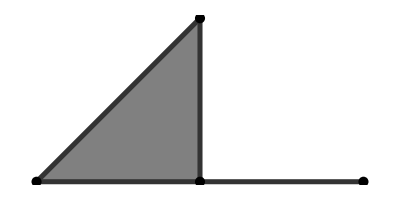

```mathematica
showCC2D[testCC]
```

Here is a 3D cell complex representing a cube:

```mathematica
testCC2={
(* 0-cells: point XYZ coordinates *)
{{0,0,0},{0,0,5},{0,5,0},{0,5,5},{5,0,0},{5,0,5},{5,5,0},{5,5,5}},
(* 1-cells: edges, each as a pair of indices of the end points of that edge *)
{{1,5},{2,6},{3,7},{4,8},{1,3},{2,4},{5,7},{6,8},{1,2},{3,4},{5,6},{7,8}},
(* 2-cells: faces, each as a list of indicies of the edges bounding that face *)
{{5,6,9,10},{7,8,11,12},{1,2,9,11},{3,4,10,12},{1,5,7,3},{2,6,8,4}},
(* 3-cells: cubes, each as a list of indicies of the faces bounding that cube *)
{{1,2,3,4,5,6}}};
```

Visualize this 3D cell complex with the showCC3D function in the Helper:

```mathematica
showCC3D[testCC2]
```

-Graphics3D-

### Conversion from binary pictures [12 pts]

Algorithm 1: [4 pts] Create a function that converts a 2D binary picture to a 2D cell complex. Your function should take in a single input (a 2-dimensional array with 0s and 1s), and output a cell complex in the above format. You may use either one of the two approaches introduced in the lecture (e.g., consistent with either 8-connectivity or 4-connectivity of the object in the binary picture).

Hint: You code should visit each pixel in the image and create new cells when appropriate. Make sure you do not re-create the same cell twice. To avoid duplication, you will need to store and retrieve the indices of 0-cells, 1-cells, 2-cells, etc as you move across the image. See lecture slides for an example of how to do so.

```mathematica
(*translation2D: zero-cell,zero-cll,one-cell(edge)*)
(*first is left edge, 2nd top edge, 3rd right edge, 4th lower edge*)
translation2D={{{-1,-1},{-1,1},{-1,0}},{{-1,1},{1,1},{0,1}},
{{1,1},{1,-1},{1,0}},{{1,-1},{-1,-1},{0,-1}}};
```

```mathematica
buildCC2D[array_]:=Module[{usedArr,n,m,i,j,cc,edgeIndices,zeroCell1,zeroCell2,oneCell,totalZeroCells,totalOneCells,totalTwoCells},
{n,m}=Dimensions[array];
(*usedArr: {visited,(its index)}*)
usedArr=Table[{False,-1},{i,1,2*m+1,1},{j,1,2*n+1,1}];
cc=Table[{},{i,3}];(*this is the 2d array that documents whether the 0,1,2-cells have been used*)
totalZeroCells=0;
totalOneCells=0;
totalTwoCells=0;
Do[
edgeIndices={};
If[array⟦y,x⟧==1,
For[i=1,i≤4,i++,
(*position = arithmetic+translation*)
zeroCell1={2*x,2*y}+translation2D⟦i⟧⟦1⟧;
zeroCell2={2*x,2*y}+translation2D⟦i⟧⟦2⟧;
oneCell={2*x,2*y}+translation2D⟦i⟧⟦3⟧;

cc⟦1⟧=If[usedArr⟦zeroCell1⟦1⟧,zeroCell1⟦2⟧⟧⟦1⟧==False,usedArr⟦zeroCell1⟦1⟧,zeroCell1⟦2⟧⟧⟦1⟧=True;(*marked*)
(*get index of this zerocell*)
totalZeroCells+=1;(*increment zerocell count*)
usedArr⟦zeroCell1⟦1⟧,zeroCell1⟦2⟧⟧⟦2⟧=totalZeroCells;
Append[cc⟦1⟧,zeroCell1],
cc⟦1⟧];

cc⟦1⟧=If[usedArr⟦zeroCell2⟦1⟧,zeroCell2⟦2⟧⟧⟦1⟧==False,
usedArr⟦zeroCell2⟦1⟧,zeroCell2⟦2⟧⟧⟦1⟧=True;(*marked*)
totalZeroCells+=1;
usedArr⟦zeroCell2⟦1⟧,zeroCell2⟦2⟧⟧⟦2⟧=totalZeroCells;
Append[cc⟦1⟧,zeroCell2],
cc⟦1⟧];

cc⟦2⟧=If[usedArr⟦oneCell⟦1⟧,oneCell⟦2⟧⟧⟦1⟧==False,
usedArr⟦oneCell⟦1⟧,oneCell⟦2⟧⟧⟦1⟧=True;(*marked*)
totalOneCells+=1;
edgeIndices=Append[edgeIndices,totalOneCells];
usedArr⟦oneCell⟦1⟧,oneCell⟦2⟧⟧⟦2⟧=totalOneCells;
Append[cc⟦2⟧,{usedArr⟦zeroCell1⟦1⟧,zeroCell1⟦2⟧⟧⟦2⟧,usedArr⟦zeroCell2⟦1⟧,zeroCell2⟦2⟧⟧⟦2⟧}],
edgeIndices=Append[edgeIndices,usedArr⟦oneCell⟦1⟧,oneCell⟦2⟧⟧⟦2⟧];
cc⟦2⟧];
];(*end for*)
cc⟦3⟧=If[usedArr⟦2*x,2*y⟧⟦1⟧==False ,
usedArr⟦2*x,2*y⟧⟦1⟧=True;
totalTwoCells+=1;
usedArr⟦2*x,2*y⟧⟦2⟧=totalTwoCells;
Append[cc⟦3⟧,edgeIndices],
cc⟦3⟧];
##&[],##&[]];
,{x,m},{y,n}];
cc
]
```

Testing: [2pts] Test your functions with the following examples (and feel free to create your own), and check your results with the provided pictures (both 8- and 4- connectivity results are shown on the left and right)

Example 1:

```mathematica
arrC={{0,0,1,1,1},{1,1,0,1,1},{0,0,1,1,1}};
```

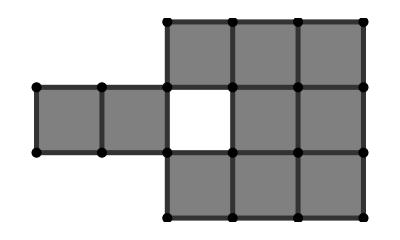

```mathematica
showCC2D[buildCC2D[arrC]]
```

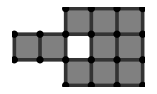
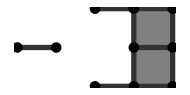

Example 2:

```mathematica
arrRing={{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,1,1},{1,1,0,0,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}};
```

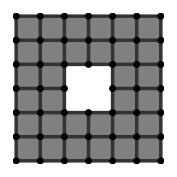
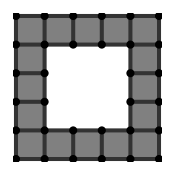

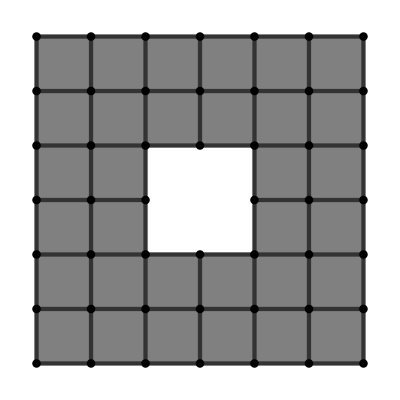

```mathematica
showCC2D[buildCC2D[arrRing]]
```

Example 3: load in the "horse_64.png", and use threshold 100 to create a binary picture.

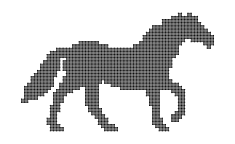
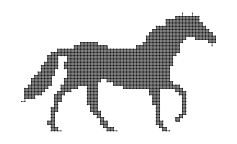

-Graphics-

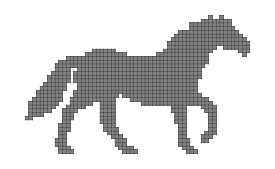

```mathematica
Import["horse_64.png"]
img=PNGtoGray["horse_64.png"];
threshold[img_, val_]:=Map[If[#>val,1,0]&,img,{2}];
bimg = threshold[img,100];
showCC2D[buildCC2D[bimg]]
```

```mathematica
thinExhaustive[buildCC2D[bimg]]
```

$Aborted

Algorithm 2: [4 pts] Create a function that converts a 3D binary picture to a 3D cell complex. Your function should take in a single input (a 3-dimensional array with 0s and 1s), and output a cell complex in the above format. You may use either one of the two approaches introduced in the lecture (e.g., consistent with either 26-connectivity or 6-connectivity of the object in the binary picture).

```mathematica
(*form:edge,edge,edge,edge,block (1c,1c,1c,1c,2c)*)
(*Inside edge:node,node,edge*)
translation2D={{{-1,-1},{-1,1},{-1,0}},{{-1,1},{1,1},{0,1}},
{{1,1},{1,-1},{1,0}},{{1,-1},{-1,-1},{0,-1}}};
translation3D={
(*translation on x axis*)
{{-1,0,0},{1,0,0}},
(*translation on y axis*)
{{0,-1,0},{0,1,0}},
(*translation on x axis*)
{{0,0,-1},{0,0,1}}
};
```

```mathematica
buildCC3D[array_]:=
Module[{usedArr,d1,d2,d3,i,j,k,t1,t2,a1,a2,cc,edgeIndices,blockIndices,zeroCell1,zeroCell2,oneCell,twoCell,totalZeroCells,totalOneCells,totalTwoCells,totalThreeCells},
{d1,d2,d3}=Dimensions[array];
(*usedArr: {visited,(its index)}*)
usedArr=Table[{False,-1},{i,1,2*d1+1,1},{j,1,2*d2+1,1},{k,1,2*d3+1,1}];
cc=Table[{},{i,4}];
(*this is the 2d array that documents whether the 0,1,2-cells have been used*)
totalZeroCells=0;
totalOneCells=0;
totalTwoCells=0;
totalThreeCells=0;
Do[
If[array⟦x,y,z⟧==1,
blockIndices={};
For[t1=1,t1≤3,t1++,
For[t2=1,t2≤2,t2++,
edgeIndices={};
twoCell={2*x,2*y,2*z}+translation3D⟦t1⟧⟦t2⟧;
For[i=1,i≤4,i++,
(*position = arithmetic+translation*)
zeroCell1={2*x,2*y,2*z}+translation3D⟦t1⟧⟦t2⟧+Which[t1==1,{0,translation2D⟦i⟧⟦1⟧⟦1⟧,translation2D⟦i⟧⟦1⟧⟦2⟧},
t1==2,{translation2D⟦i⟧⟦1⟧⟦1⟧,0,translation2D⟦i⟧⟦1⟧⟦2⟧},
t1==3,{translation2D⟦i⟧⟦1⟧⟦1⟧,translation2D⟦i⟧⟦1⟧⟦2⟧,0}];
zeroCell2={2*x,2*y,2*z}+translation3D⟦t1⟧⟦t2⟧+Which[t1==1,{0,translation2D⟦i⟧⟦2⟧⟦1⟧,translation2D⟦i⟧⟦2⟧⟦2⟧},
t1==2,{translation2D⟦i⟧⟦2⟧⟦1⟧,0,translation2D⟦i⟧⟦2⟧⟦2⟧},
t1==3,{translation2D⟦i⟧⟦2⟧⟦1⟧,translation2D⟦i⟧⟦2⟧⟦2⟧,0}];
oneCell={2*x,2*y,2*z}+translation3D⟦t1⟧⟦t2⟧+Which[t1==1,{0,translation2D⟦i⟧⟦3⟧⟦1⟧,translation2D⟦i⟧⟦3⟧⟦2⟧},
t1==2,{translation2D⟦i⟧⟦3⟧⟦1⟧,0,translation2D⟦i⟧⟦3⟧⟦2⟧},
t1==3,{translation2D⟦i⟧⟦3⟧⟦1⟧,translation2D⟦i⟧⟦3⟧⟦2⟧,0}];
(*
Print[zeroCell1,",",zeroCell2,",",oneCell];*)
cc⟦1⟧=If[usedArr⟦zeroCell1⟦1⟧,zeroCell1⟦2⟧,zeroCell1⟦3⟧⟧⟦1⟧==False,usedArr⟦zeroCell1⟦1⟧,zeroCell1⟦2⟧,zeroCell1⟦3⟧⟧⟦1⟧=True;(*marked*)
(*get index of this zerocell*)
totalZeroCells+=1;(*increment zerocell count*)
usedArr⟦zeroCell1⟦1⟧,zeroCell1⟦2⟧,zeroCell1⟦3⟧⟧⟦2⟧=totalZeroCells;
Append[cc⟦1⟧,zeroCell1],
cc⟦1⟧];

cc⟦1⟧=If[usedArr⟦zeroCell2⟦1⟧,zeroCell2⟦2⟧,zeroCell2⟦3⟧⟧⟦1⟧==False,
usedArr⟦zeroCell2⟦1⟧,zeroCell2⟦2⟧,zeroCell2⟦3⟧⟧⟦1⟧=True;(*marked*)
totalZeroCells+=1;
usedArr⟦zeroCell2⟦1⟧,zeroCell2⟦2⟧,zeroCell2⟦3⟧⟧⟦2⟧=totalZeroCells;
Append[cc⟦1⟧,zeroCell2],
cc⟦1⟧];

cc⟦2⟧=If[usedArr⟦oneCell⟦1⟧,oneCell⟦2⟧,oneCell⟦3⟧⟧⟦1⟧==False,
usedArr⟦oneCell⟦1⟧,oneCell⟦2⟧,oneCell⟦3⟧⟧⟦1⟧=True;(*marked*)
totalOneCells+=1;
edgeIndices=Append[edgeIndices,totalOneCells];
usedArr⟦oneCell⟦1⟧,oneCell⟦2⟧,oneCell⟦3⟧⟧⟦2⟧=totalOneCells;
Append[cc⟦2⟧,{usedArr⟦zeroCell1⟦1⟧,zeroCell1⟦2⟧,zeroCell1⟦3⟧⟧⟦2⟧,usedArr⟦zeroCell2⟦1⟧,zeroCell2⟦2⟧,zeroCell2⟦3⟧⟧⟦2⟧}],
edgeIndices=Append[edgeIndices,usedArr⟦oneCell⟦1⟧,oneCell⟦2⟧,oneCell⟦3⟧⟧⟦2⟧];
cc⟦2⟧];
];(*end for*)
cc⟦3⟧=If[usedArr⟦twoCell⟦1⟧,twoCell⟦2⟧,twoCell⟦3⟧⟧⟦1⟧==False ,
usedArr⟦twoCell⟦1⟧,twoCell⟦2⟧,twoCell⟦3⟧⟧⟦1⟧=True;
totalTwoCells+=1;
usedArr⟦twoCell⟦1⟧,twoCell⟦2⟧,twoCell⟦3⟧⟧⟦2⟧=totalTwoCells;
blockIndices=Append[blockIndices,totalTwoCells];
Append[cc⟦3⟧,edgeIndices],
blockIndices=Append[blockIndices,
usedArr⟦twoCell⟦1⟧,twoCell⟦2⟧,twoCell⟦3⟧⟧⟦2⟧];
cc⟦3⟧];
];
];
cc⟦4⟧=If[usedArr⟦2*x,2*y,2*z⟧⟦1⟧==False ,
usedArr⟦2*x,2*y,2*z⟧⟦1⟧=True;
totalThreeCells+=1;
usedArr⟦2*x,2*y,2*z⟧⟦2⟧=totalThreeCells;
Append[cc⟦4⟧,blockIndices],
cc⟦4⟧];
##&[],##&[]];
,{x,d1},{y,d2},{z,d3}];
cc
]
```

```mathematica
showCC3D[buildCC3D[{{{1,0}}}]]
(*Dimensions[{{{1,1}}}]*)
```

-Graphics3D-

```mathematica
Dimensions[{{{1,3}}}]
```

{1,1,2}

Testing: [2pts] Test your functions with the following examples (and feel free to create your own), and check your results with the provided pictures (both 26- and 6- connectivity results are shown below on the left and right)

Example 1:

```mathematica
arrC3D={
{{0,0},{0,0},{1,0},{1,0},{1,0}},
{{1,0},{1,0},{0,0},{1,0},{1,0}},
{{0,0},{0,0},{1,0},{1,0},{1,0}}
};
```

```mathematica
showCC3D[buildCC3D[arrC3D]]
```

-Graphics3D-

```mathematica
arrC3D[[1,3,1]]==1
arrC3D[[1,3,2]]≤0+1
```

True

True

```mathematica
-Graphics3D--Graphics3D-
```

Example 2:

```mathematica
arrRing3D={{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},{{1,1},{1,1},{1,1},{0,0},{0,0},{1,1},{1,1},{1,1}},{{1,1},{1,1},{1,1},{0,0},{0,0},{1,1},{1,1},{1,1}},{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}};
```

```mathematica
Dimensions[arrRing3D]
```

{8,8,2}

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
showCC3D[buildCC3D[arrRing3D]]
```

-Graphics3D-

Example 3: load the "tshape.dat" in the folder (using Get command, which will return a 3D binary picture).

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
tshape=Get["tshape.dat"]
```

{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},30,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{1},{1},26,{1},{1},{1}}
 |  |  |  |

{}

```mathematica
cct=buildCC3D[tshape];
```

```mathematica
showCC3D[buildCC3D[tshape]]
```

-Graphics3D-

### Thinning [10 pts]

Algorithm 3: [4 pts] Create a function that performs exhaustive, parallel thinning on a cell complex (all simple pairs are removed in each iteration, without preserving the medial cells). The function takes in a cell complex (which could be in 2D or 3D), and outputs another cell complex that is the resulting skeleton.

```mathematica
getNumParent[cc_]:=Module[{pNumber,parentNumberTable,numParentTable,parentIndex,parentTable,childTable,killFirstTable,origIndexTable,origLvlTable,isExcludeTable,isIn,rmTable,result},
(*return all the parent number for cells that has dimension[cc]-1*)
(*format: 
 1) parentNumberTable: # parents, 
	2) parentTable: parent indeices in the above level,
	  3) childTable: child indices,
		4) killFirstTable: boolean kill first,
		  5) origIndexTable: orignal index, 
			6) origLvlTable: its level
		   7) isExcludeTable: boolean is excluded
*)
parentNumberTable=Table[{0,{},{},False,-1,-1,False},{i,Dimensions[cc][[1]]},{j,Dimensions[cc⟦i⟧]⟦1⟧}];

numParentTable=Table[0,{i,Dimensions[cc]⟦1⟧},{j,Dimensions[cc⟦i⟧]⟦1⟧}];
parentTable=Table[{},{i,Dimensions[cc]⟦1⟧},{j,Dimensions[cc⟦i⟧]⟦1⟧}];
childTable=Table[If[i≠1,cc⟦i,j⟧,{}],{i,Dimensions[cc][[1]]},{j,Dimensions[cc⟦i⟧]⟦1⟧}];
killFirstTable=Table[False,{i,Dimensions[cc]⟦1⟧},{j,Dimensions[cc⟦i⟧]⟦1⟧}];
origIndexTable=Table[j,{i,Dimensions[cc]⟦1⟧},{j,Dimensions[cc⟦i⟧]⟦1⟧}];
origLvlTable=Table[i,{i,Dimensions[cc]⟦1⟧},{j,Dimensions[cc⟦i⟧]⟦1⟧}];
isExcludeTable=Table[False,{i,Dimensions[cc]⟦1⟧},{j,Dimensions[cc⟦i⟧]⟦1⟧}];

For[i=Dimensions[cc]⟦1⟧,i>1,i--,
(*for each level*)
For[j=1,j≤Dimensions[cc⟦i⟧]⟦1⟧,j++,
(*for each list in each level*)
For[k=1,k≤Dimensions[cc⟦i,j⟧]⟦1⟧,k++,
(*for each element in each list in each level*)
parentTable⟦i-1,cc⟦i,j,k⟧⟧=Append[parentTable⟦i-1,cc⟦i,j,k⟧⟧,j];
numParentTable⟦i-1,cc⟦i,j,k⟧⟧++;
];];];

result={numParentTable,parentTable,childTable,killFirstTable,origIndexTable,origLvlTable,isExcludeTable};
result
]

getIsoTable[parentTable_]:=Module[{isoTable},
isoTable=ParallelMap[If[#⟦1⟧==0,0,-1]&,parentTable,{3}];
isoTable
]

removeKilledParentIndex[numParentTable_,parentTable_,childTable_,killFirstTable_,cc_]:=Module[{childIndex,selfIndex,temp,newChildTable,newParentable,newNumParentTable,result},
(*Remove killed parent's index and adjust parent numbers*)

(*child needs to update new parent list*)
newParentable=ParallelTable[If[i<Dimensions[cc]⟦1⟧,
Select[parentTable⟦i,j⟧,killFirstTable⟦i+1,#⟧==False&],
parentTable⟦i,j⟧],{i,Dimensions[cc]⟦1⟧},{j,Dimensions[cc⟦i⟧]⟦1⟧}];

newNumParentTable=ParallelTable[Length[newParentable⟦i,j⟧],{i,Dimensions[cc]⟦1⟧},{j,Dimensions[cc⟦i⟧]⟦1⟧}];
(*parent needs to empty its child list*)

newChildTable=ParallelTable[If[i>1&&killFirstTable⟦i,j⟧==True,
{},childTable⟦i,j⟧],{i,Dimensions[cc]⟦1⟧},{j,Dimensions[cc⟦i⟧]⟦1⟧}];

result={newNumParentTable,newParentable,newChildTable};
result
];


updateDisjoint[numParentTable_,killFirstTable_,childTable_,excludeTable_,cc_]:=Module[{newKillFirstTable,childIndex,spNum,result,spPairs},
spNum=0;
newKillFirstTable=killFirstTable;
spPairs={};
(*Here we update the disjoint information*)
For[i=Dimensions[numParentTable]⟦1⟧,i>1,i--,
(*Print["Floor: ",i];*)
For[j=1,j≤Dimensions[numParentTable⟦i⟧]⟦1⟧,j++,
(*Print["Component: ",j];*)
For[k=1,k≤Length[childTable⟦i,j⟧],k++,
(*Print[Length[cc⟦i⟧⟦j⟧]];*)
childIndex=childTable⟦i,j⟧⟦k⟧;
If[numParentTable⟦i-1,childIndex⟧==1&&newKillFirstTable⟦i,j⟧==False&&newKillFirstTable⟦i-1,childIndex⟧==False&&excludeTable⟦i-1,childIndex⟧==False&&excludeTable⟦i,j⟧==False,
(*only kill if it's not excluded*)
spNum++;
newKillFirstTable⟦i,j⟧=True;
newKillFirstTable⟦i-1,childIndex⟧=True;
spPairs=Append[spPairs,{{i,j},{i-1,childIndex}}];
##&[],
##&[]];
];
];

];
result={newKillFirstTable,spNum,spPairs};
result
]
```

```mathematica
constructMapAndCC[killFirstTable_,cc_]:=Module[{indexMap,newCC,oldIndex,elemIndex,result},
(*{old index,new index}*)
indexMap=Table[{j,-1},{i,Dimensions[cc][[1]]},{j,Dimensions[cc⟦i⟧]⟦1⟧}];
(*Mark all its original index*)

(*Append if it is not removed;mark*)
newCC=cc;
For[i=1,i≤Dimensions[cc]⟦1⟧,i++,
elemIndex=1;
newCC⟦i⟧={};
For[j=1,j≤Length[cc⟦i⟧],j++,
If[killFirstTable⟦i,j⟧==False,
(*this element is not killed*)
newCC⟦i⟧=Append[newCC⟦i⟧,cc⟦i,j⟧];
indexMap⟦i,j⟧⟦2⟧=elemIndex;
elemIndex++;
##&[],
##&[]];
];
];
result={newCC,indexMap};
result
]
```

```mathematica
updateIndex[indexMap_,newCC_]:=Module[{newerCC},
newerCC=newCC;
(*Print["omg?"];*)
For[i=2,i≤Dimensions[newCC]⟦1⟧,i++,
For[j=1,j≤Length[newCC⟦i⟧],j++,
For[k=1,k≤Length[newCC⟦i,j⟧],k++,
(*Print["Set at ",i,"th row and ",j,"th elem's ",k,"th comp from ", newCC⟦i,j⟧, " to ",indexMap⟦i-1,newCC⟦i,j,k⟧⟧⟦2⟧];*)
newerCC⟦i,j,k⟧=indexMap⟦i-1,newCC⟦i,j,k⟧⟧⟦2⟧;
];
];
];
(*Print["omg2?"];*)
newerCC
]
```

```mathematica
restoreAfterEThinning2[killFirstTable_,cc_]:=Module[{newCC,indexMap,newerCC},
{newCC,indexMap}=constructMapAndCC[killFirstTable,cc];
newerCC=updateIndex[indexMap,newCC];
newerCC
]
```

Hints:
1. To easily identify simple pairs, it is helpful to write a helper function that computes a table that stores, at each k-cell x, the number of (k+1)-cells (i.e., "parents") containing x on their boundary. Try to compute this parent table using a single pass over all the cells. With the table, you can identify a cell x as a simple cell if any of its children cells has exactly 1 parent. Again, you should be able to identify all simple pairs in a single pass over all the cells. Now, think about how to efficiently update the parent table after each iteration of thinning (without re-computing it by visiting all remaining cells).

2. Instead of explicitly removing the cells from the cell complex data structure at each iteration, a more efficient way is simply keeping a True/False tag at each cell indicating whether it is still in the complex. After thinning stops, you can then use these tags to remove all non-existent cells from the data structure in one pass. 

3. Be careful in updating the cell indices when removing the cells from the cell complex. For example, if the first cell in the list of k-cells is removed, any (k+1)-cell that uses the second cell in the original list of k-cells should now change the index of that k-cell from 2 to 1. Again, think about how to do so efficiently.

```mathematica
thinExhaustive[cc_]:=Module[{numPT,pt,ct,kft,oit,olt,isE,isoTable,spNum,spPairs,thinnedCC},
{numPT,pt,ct,kft,oit,olt,isE}=getNumParent[cc];
While[True,
{kft,spNum,spPairs}=updateDisjoint[numPT,kft,ct,isE,cc];
If[spNum==0,
Break[];
##&[],
##&[]];
{numPT,pt,ct}=removeKilledParentIndex[numPT,pt,ct,kft,cc];

];

(*result={numPT,pt,ct,kft};
result*)
thinnedCC=restoreAfterEThinning2[kft,cc];
thinnedCC
]
```

Testing: [2pts] Test your function with 2D and 3D examples you have created above. Check your result (they should have the same topology as the original complexes while cannot be thinned further). Use the showCC2D, showCC3D functions to show the skeleton on top of the original complex.

```mathematica
cc1=buildCC2D[arrC];
cc2=buildCC2D[arrRing];
```

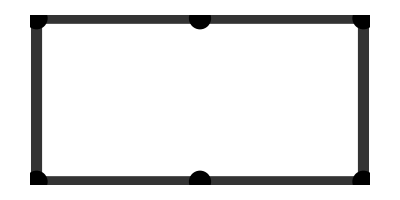

```mathematica
showCC2D[thinExhaustive[cc1]]
```

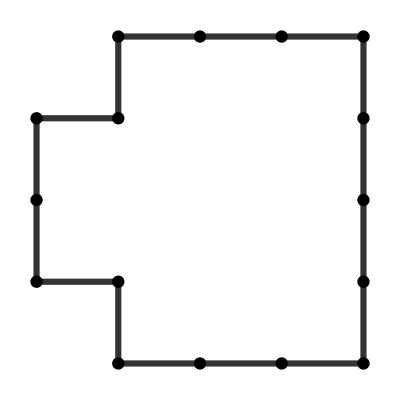

```mathematica
showCC2D[thinExhaustive[cc2]]
```

```mathematica
q=thinExhaustive[buildCC3D[arrRing3D]];
```

```mathematica
showCC3D[q]
```

-Graphics3D-

```mathematica
thinTS=thinExhaustive[buildCC3D[tshape]];
```

$Aborted

Algorithm 4: [2 pts] Modify your function above to perform thinning while protecting the medial cells. In addition to a cell complex, your function will take in an additional list containing the thresholds. The thresholds will be a list of pairs, so that the n-th pair are the thresholds for the absolute and relative differences between the isolation and removal iterations for the n-cells. For example, thinning a 2D complex would call thin[cc,{{5,0.5}}], and thinning a 3D complex may call thin[cc,{{5,0.5},{∞,1}}].

Hint: You can use the parent table you created for your exhaustive thinning function to quickly identify the isolated cells. Think about how to identify the isolated cells in an efficient way, without having to go through all the cells at each iteration (since you know exactly which cells are becoming "isolated" when you remove the simple pairs).

```mathematica
startIsoTable[parentTable_,cc_]:=Module[{isoTable},
isoTable=ParallelTable[If[Length[parentTable⟦i,j⟧]==0,0,Null],{i,Dimensions[cc]⟦1⟧},{j,Dimensions[cc⟦i⟧]⟦1⟧}];
isoTable
]
```

```mathematica
setIsoTable[parentTable_,k_,isoTable_,cc_]:=Module[{newIsoTable},
(*set newly isolated cells to k (newly isolated iff cell in isoTable is currently Null)*)
newIsoTable=ParallelTable[If[Length[parentTable⟦i,j⟧]==0,If[NumberQ[isoTable⟦i,j⟧],isoTable⟦i,j⟧,k],Null],{i,Dimensions[cc]⟦1⟧},{j,Dimensions[cc⟦i⟧]⟦1⟧}];
newIsoTable
]
```

```mathematica
oneCellExclusionTest2[killFirstTable_,isoTable_,excludeTable_,parentTable_,k_,t1ABS_,t1REL_,spNum_,spPairs_]:=Module[{newkft,newSPNum,result,newExcludeTable,oneCellIndex,pairedCellIndex,oneCellLoc,pairedCellLoc,test,positionTemp1Cell},
newkft=killFirstTable;
newSPNum=spNum;
newExcludeTable=excludeTable;


For[i=1,i≤Length[spPairs],i++,
(*locate one cells*)
positionTemp1Cell=Position[Map[#⟦1⟧&,spPairs⟦i⟧],2];
If[Length[positionTemp1Cell]≠0,
oneCellIndex=positionTemp1Cell⟦1,1⟧;
pairedCellIndex=If[oneCellIndex==1,2,1];
oneCellLoc=spPairs⟦i,oneCellIndex⟧;
pairedCellLoc=spPairs⟦i,pairedCellIndex⟧;
(*if first object in the pair's first index is 2, this is a one cell*)
test=NumberQ[isoTable⟦oneCellLoc⟦1⟧,oneCellLoc⟦2⟧⟧]&&k-isoTable⟦oneCellLoc⟦1⟧,oneCellLoc⟦2⟧⟧>t1ABS&&1-isoTable⟦oneCellLoc⟦1⟧,oneCellLoc⟦2⟧⟧/k>t1REL;
(*it requires that one-cells we are testing are isolated cells, so that I(x) is defined, otherwise it is Null, which means it is not isolated, and we can safely remove this simple pair*)
If[test==True,
newkft⟦oneCellLoc⟦1⟧,oneCellLoc⟦2⟧⟧=False;
newkft⟦pairedCellLoc⟦1⟧,pairedCellLoc⟦2⟧⟧=False;
newExcludeTable⟦oneCellLoc⟦1⟧,oneCellLoc⟦2⟧⟧=True;
newExcludeTable⟦pairedCellLoc⟦1⟧,pairedCellLoc⟦2⟧⟧=True;
newSPNum--;
##&[],##&[]];
##&[],##&[]];
];
result={newkft,newExcludeTable,newSPNum};
result
]
```

```mathematica
thin[cc_,thresholds_]:=Module[{pTable,kthIter,t1ABS,t1REL,isoTable,excludeTable,spNum,spPairs
,numPT,pt,ct,kft,oit,olt,isE,thinnedCC},
t1ABS=thresholds⟦1,1⟧;t1REL=thresholds⟦1,2⟧;
(*setup the threshold so don't retrieve by indexing*)
{numPT,pt,ct,kft,oit,olt,isE}=getNumParent[cc];
(*get basic needs for later use*)
isoTable=startIsoTable[pt,cc];
(*mark 0 if cell has no parents, else mark NULL*)

kthIter=1;(*current increment*)
(*isolated cells:cells that have no parent*)
While[True,
{kft,spNum,spPairs}=updateDisjoint[numPT,kft,ct,isE,cc];
{kft,isE,spNum}=oneCellExclusionTest2[kft,isoTable,isE,pt,kthIter,t1ABS,t1REL,spNum,spPairs];
If[spNum==0,
Break[];
##&[],
##&[]];
{numPT,pt,ct}=removeKilledParentIndex[numPT,pt,ct,kft,cc];
isoTable=setIsoTable[pt,kthIter,isoTable,cc];
kthIter++;
];

thinnedCC=restoreAfterEThinning2[kft,cc];
thinnedCC
]
```

```mathematica
twoCellExclusionTest[killFirstTable_,isoTable_,excludeTable_,parentTable_,k_,t2ABS_,t2REL_,spNum_,spPairs_]:=Module[{newkft,newSPNum,result,newExcludeTable,twoCellIndex,pairedCellIndex,twoCellLoc,pairedCellLoc,test,positionTemp2Cell},
newkft=killFirstTable;
newSPNum=spNum;
newExcludeTable=excludeTable;


For[i=1,i≤Length[spPairs],i++,
(*locate two cells*)
positionTemp2Cell=Position[Map[#⟦1⟧&,spPairs⟦i⟧],3];
If[Length[positionTemp2Cell]≠0,
twoCellIndex=positionTemp2Cell⟦1,1⟧;
pairedCellIndex=If[twoCellIndex==1,2,1];
twoCellLoc=spPairs⟦i,twoCellIndex⟧;
pairedCellLoc=spPairs⟦i,pairedCellIndex⟧;
(*if first object in the pair's first index is 2, this is a one cell*)
test=NumberQ[isoTable⟦twoCellLoc⟦1⟧,twoCellLoc⟦2⟧⟧]&&k-isoTable⟦twoCellLoc⟦1⟧,twoCellLoc⟦2⟧⟧>t2ABS&&1-isoTable⟦twoCellLoc⟦1⟧,twoCellLoc⟦2⟧⟧/k>t2REL;
(*it requires that one-cells we are testing are isolated cells, so that I(x) is defined, otherwise it is Null, which means it is not isolated, and we can safely remove this simple pair*)
If[test==True,
newkft⟦twoCellLoc⟦1⟧,twoCellLoc⟦2⟧⟧=False;
newkft⟦pairedCellLoc⟦1⟧,pairedCellLoc⟦2⟧⟧=False;
newExcludeTable⟦twoCellLoc⟦1⟧,twoCellLoc⟦2⟧⟧=True;
newExcludeTable⟦pairedCellLoc⟦1⟧,pairedCellLoc⟦2⟧⟧=True;
newSPNum--;
##&[],##&[]];
##&[],##&[]];
];
result={newkft,newExcludeTable,newSPNum};
result
]
```

```mathematica
thin3D[cc_,thresholds_]:=Module[{pTable,kthIter,t1ABS,t1REL,t2ABS,t2REL,isoTable,excludeTable,spNum,spPairs
,numPT,pt,ct,kft,oit,olt,isE,thinnedCC},
t1ABS=thresholds⟦1,1⟧;t1REL=thresholds⟦1,2⟧;
t2ABS=thresholds⟦2,1⟧;t2REL=thresholds⟦2,2⟧;
(*setup the threshold so don't retrieve by indexing*)
{numPT,pt,ct,kft,oit,olt,isE}=getNumParent[cc];
(*get basic needs for later use*)
isoTable=startIsoTable[pt,cc];
(*mark 0 if cell has no parents, else mark NULL*)

kthIter=1;(*current increment*)
(*isolated cells:cells that have no parent*)
While[True,
{kft,spNum,spPairs}=updateDisjoint[numPT,kft,ct,isE,cc];
{kft,isE,spNum}=twoCellExclusionTest[kft,isoTable,isE,pt,kthIter,t2ABS,t2REL,spNum,spPairs];
{kft,isE,spNum}=oneCellExclusionTest2[kft,isoTable,isE,pt,kthIter,t1ABS,t1REL,spNum,spPairs];
If[spNum==0,
Break[];
##&[],
##&[]];
{numPT,pt,ct}=removeKilledParentIndex[numPT,pt,ct,kft,cc];
isoTable=setIsoTable[pt,kthIter,isoTable,cc];
kthIter++;
];

thinnedCC=restoreAfterEThinning2[kft,cc];
thinnedCC
]
```

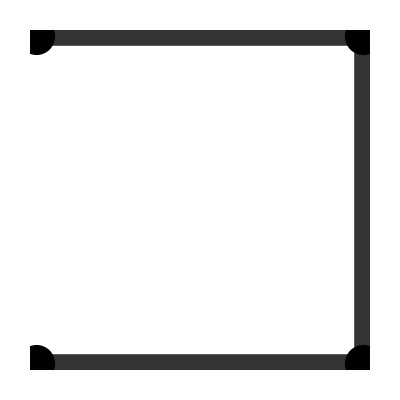

```mathematica
showCC2D[thin[buildCC2D[{{1}}],{{0,0.0}}]]
```

Testing: [2pts] Test your function with the horse example in 2D and the tShape example in 3D (which you have converted from binary pictures). Check your result with the following pictures at these parameter settings:

2D horse example:

-Graphics-

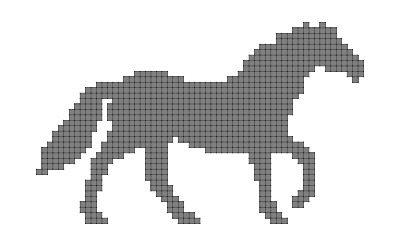

```mathematica
Import["horse_64.png"]
img=PNGtoGray["horse_64.png"];
threshold[img_, val_]:=Map[If[#>val,1,0]&,img,{2}];
bimg = threshold[img,100];
showCC2D[buildCC2D[bimg]]
```

```mathematica
horse8=buildCC2D[bimg];
```

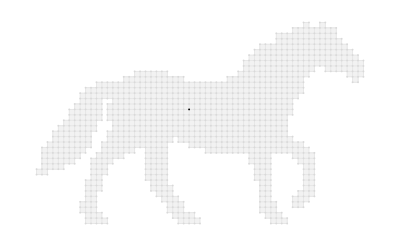

```mathematica
showCC2D[thin[horse8,{{∞,1}}],horse8]
```

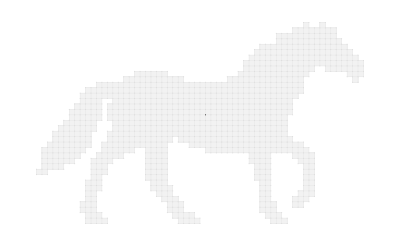

```mathematica
showCC2D[thin[horse8,{{∞,1}}],horse8]
```

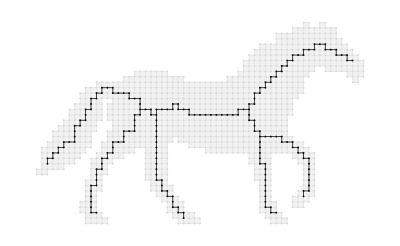

```mathematica
showCC2D[thin[horse8,{{4,.4}}],horse8]
```

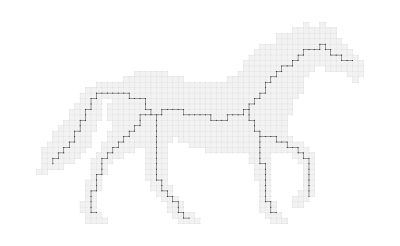

```mathematica
showCC2D[thin[horse8,{{4,0.4}}],horse8]
```

3D Tshape example:

```mathematica
showCC3D[thin[tShape26,{{∞,1},{∞,1}}],tShape26]
```

-Graphics3D-

```mathematica
showCC3D[thin3D[cct,{{∞,1},{∞,1}}],cct]
```

-Graphics3D-

```mathematica
showCC3D[thin[tShape26,{{∞,1},{5,.5}}],tShape26]
```

-Graphics3D-

```mathematica
showCC3D[thin3D[cct,{{∞,1},{5,.5}}],cct]
```

-Graphics3D-

```mathematica
showCC3D[thin[tShape26,{{4,.4},{∞,1}}],tShape26]
```

-Graphics3D-

```mathematica
showCC3D[thin3D[cct,{{4,.4},{∞,1}}],cct]
```

-Graphics3D-

```mathematica
showCC3D[thin[tShape26,{{4,.4},{5,.5}}],tShape26]
```

-Graphics3D-

```mathematica
showCC3D[thin3D[cct,{{4,.4},{5,.5}}],cct]
```

-Graphics3D-

```mathematica
ccR=buildCC3D[arrRing3D];
```

```mathematica
showCC3D[thin3D[ccR,{{1,0.2},{0,0}}],ccR]
```

-Graphics3D-

## Problems

Use your thinning code to compute skeletons of these 2D and 3D shapes.

### Leaf epidermis [2 pts]

Problem 1: [1 pts] See image in "epidermis.png" shown on the left. Compute a curve skeleton that best represents the curved features in the image (an example is on the right). Use the showCC2DImg function to view skeletons overlayed on the image.

```mathematica
-Graphics--Graphics-
```

```mathematica
Import["epidermis.png"]
eimg=PNGtoGray["epidermis.png"];
threshold[img_, val_]:=Map[If[#>val,1,0]&,img,{2}];
```

-Graphics-

```mathematica
beimg = threshold[eimg,15]
```

{1}
 |  |  |  |

```mathematica
epidermis=buildCC2D[beimg];
```

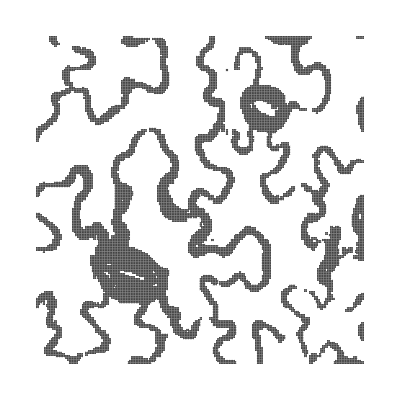

```mathematica
showCC2D[epidermis]
```

```mathematica
thinnedEpidermis=thin[epidermis,{{2,0.2}}];
```

```mathematica
showCC2DImg[thinnedEpidermis,eimg]
```

```mathematica
Show[%1181,ImageSize->Large]
```

### Micro filaments [2 pts]

Problem 2: [1 pts] See image in "filament_part.png" shown on the left. Compute a curve skeleton that best represents the line features in the image (an example is on the right).

```mathematica
-Graphics--Graphics-
```

### Human hand [2 pts]

Problem 3: [2 pts] Load the 3D binary picture in "hand.dat", and compute the three types of skeletons as shown below.

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
-Graphics3D--Graphics3D-
```

```mathematica
handDAT=Get["hand.dat"];
```

```mathematica
handCC=buildCC3D[handDAT];
```

```mathematica
thinnedHand1=thin3D[handCC,{{2,0.01},{2,0.01}}];
```

$Aborted